```mathematica
file3=<<"/Users/ruppell/Math/temp/btn.txt";
```

```mathematica
Dimensions@file3
```

{10,82,2}

```mathematica
bnunu=file3[[;;,;;,1,1]];
```

```mathematica
d[i_]:=(file3[[;;,;;,1,1]][[i]]/file3[[;;,;;,1,1]][[i,1]])
```

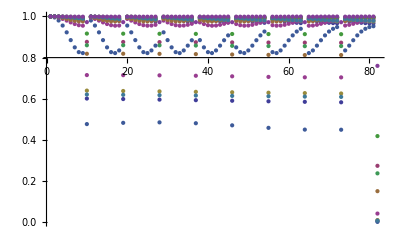

```mathematica
ListPlot[d/@Range@10,PlotRange->{{0,10},{1,0.8}}]
```